```mathematica
a=0.2;
b=1.5;
Clear[f,x,n]
f[x_,n_] = Sum[a^{-m}*Cos[b^m*Pi*x],{m,1,n}]
Animate[Plot[f[x,n],{x,-10,10},PlotRange->All],{n,1,8}]
```

{∑_(m=1)^n 0.2^-m Cos[1.5^m π x]}

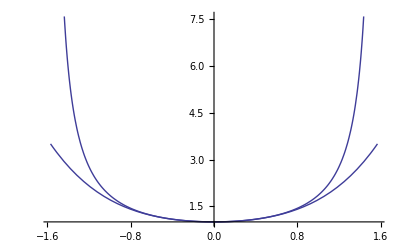

```mathematica
Clear[x]
Show[Plot[Evaluate[Normal[Series[1/Cos[x],{x,0,4}]]],{x,-Pi/2,Pi/2},PlotRange->All],
Plot[1/Cos[x],{x,-Pi/2,Pi/2}]]
```

```mathematica
f[x_,y_]:=If[x==0&& y== 0 , 0, x*y / (x^2+y^2)]
Plot3D[f[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Clear["Global`*"]
Clear[f]
```

```mathematica
f[y_] =Abs[y-1/2];
P[x_,n_] = Sum[Binomial[n,p] f[p/n]*x^p* (1-x)^(n-p),{p,0,n}];
P[x,1]
```

-(1-x-(1-x) x)/(2 (1-x) (-1+x))

{1/(2 (-1-x+x^2))(-1-x-(1-x) x+(-1+x) x+x^2-(1-x) x^2+(-1+x) x^2+(1-x) x^3-(-1+x) x^3+x (1+x-x^2)-x^2 (1+x-x^2)),1/(4 (-1-x+x^2))(-2 (1-x) x^2+2 (-1+x) x^2+4 (1-x) x^4-4 (-1+x) x^4-2 (1-x) x^5+2 (-1+x) x^5-2 (1+x-x^2)^2+2 x (1+x-x^2)^2-2 x^2 (1+x-x^2)^2),1/(6 (-1-x+x^2))(-2 (1-x)^2 x^3-2 (-1+x)^2 x^3+4 (1-x)^2 x^5+4 (-1+x)^2 x^5-2 (1-x)^2 x^6-2 (-1+x)^2 x^6-3 (1+x-x^2)^3+3 x (1+x-x^2)^3-3 x^2 (1+x-x^2)^3-(1-x)^2 x^2 (3+x-x^2)-(-1+x)^2 x^2 (3+x-x^2)-(1-x)^2 x^3 (3+x-x^2)-(-1+x)^2 x^3 (3+x-x^2)+(1-x)^2 x^4 (3+x-x^2)+(-1+x)^2 x^4 (3+x-x^2)),1/(8 (-1-x+x^2))(-4 (1+x-x^2)^4+4 x (1+x-x^2)^4-4 x^2 (1+x-x^2)^4-4 (1-x)^2 x^3 (2+x-x^2)-4 (-1+x)^2 x^3 (2+x-x^2)+8 (1-x)^2 x^5 (2+x-x^2)+8 (-1+x)^2 x^5 (2+x-x^2)-4 (1-x)^2 x^6 (2+x-x^2)-4 (-1+x)^2 x^6 (2+x-x^2)),1/(10 (-1-x+x^2))(-2 (1-x)^3 x^4 (5+2 x-2 x^2)+2 (-1+x)^3 x^4 (5+2 x-2 x^2)+4 (1-x)^3 x^6 (5+2 x-2 x^2)-4 (-1+x)^3 x^6 (5+2 x-2 x^2)-2 (1-x)^3 x^7 (5+2 x-2 x^2)+2 (-1+x)^3 x^7 (5+2 x-2 x^2)-5 (1+x-x^2)^5+5 x (1+x-x^2)^5-5 x^2 (1+x-x^2)^5-(1-x)^3 x^3 (10+5 x-4 x^2-2 x^3+x^4)+(-1+x)^3 x^3 (10+5 x-4 x^2-2 x^3+x^4)-(1-x)^3 x^4 (10+5 x-4 x^2-2 x^3+x^4)+(-1+x)^3 x^4 (10+5 x-4 x^2-2 x^3+x^4)+(1-x)^3 x^5 (10+5 x-4 x^2-2 x^3+x^4)-(-1+x)^3 x^5 (10+5 x-4 x^2-2 x^3+x^4)),1/(12 (-1-x+x^2))(-6 (1+x-x^2)^6+6 x (1+x-x^2)^6-6 x^2 (1+x-x^2)^6-6 (1-x)^3 x^4 (5+4 x-3 x^2-2 x^3+x^4)+6 (-1+x)^3 x^4 (5+4 x-3 x^2-2 x^3+x^4)+12 (1-x)^3 x^6 (5+4 x-3 x^2-2 x^3+x^4)-12 (-1+x)^3 x^6 (5+4 x-3 x^2-2 x^3+x^4)-6 (1-x)^3 x^7 (5+4 x-3 x^2-2 x^3+x^4)+6 (-1+x)^3 x^7 (5+4 x-3 x^2-2 x^3+x^4)),1/(14 (-1-x+x^2))(-7 (1+x-x^2)^7+7 x (1+x-x^2)^7-7 x^2 (1+x-x^2)^7-2 (1-x)^4 x^5 (21+14 x-11 x^2-6 x^3+3 x^4)-2 (-1+x)^4 x^5 (21+14 x-11 x^2-6 x^3+3 x^4)+4 (1-x)^4 x^7 (21+14 x-11 x^2-6 x^3+3 x^4)+4 (-1+x)^4 x^7 (21+14 x-11 x^2-6 x^3+3 x^4)-2 (1-x)^4 x^8 (21+14 x-11 x^2-6 x^3+3 x^4)-2 (-1+x)^4 x^8 (21+14 x-11 x^2-6 x^3+3 x^4)-(1-x)^4 x^4 (35+21 x-14 x^2-13 x^3+4 x^4+3 x^5-x^6)-(-1+x)^4 x^4 (35+21 x-14 x^2-13 x^3+4 x^4+3 x^5-x^6)-(1-x)^4 x^5 (35+21 x-14 x^2-13 x^3+4 x^4+3 x^5-x^6)-(-1+x)^4 x^5 (35+21 x-14 x^2-13 x^3+4 x^4+3 x^5-x^6)+(1-x)^4 x^6 (35+21 x-14 x^2-13 x^3+4 x^4+3 x^5-x^6)+(-1+x)^4 x^6 (35+21 x-14 x^2-13 x^3+4 x^4+3 x^5-x^6)),1/(16 (-1-x+x^2))(-8 (1+x-x^2)^8+8 x (1+x-x^2)^8-8 x^2 (1+x-x^2)^8-8 (1-x)^4 x^5 (14+14 x-8 x^2-11 x^3+3 x^4+3 x^5-x^6)-8 (-1+x)^4 x^5 (14+14 x-8 x^2-11 x^3+3 x^4+3 x^5-x^6)+16 (1-x)^4 x^7 (14+14 x-8 x^2-11 x^3+3 x^4+3 x^5-x^6)+16 (-1+x)^4 x^7 (14+14 x-8 x^2-11 x^3+3 x^4+3 x^5-x^6)-8 (1-x)^4 x^8 (14+14 x-8 x^2-11 x^3+3 x^4+3 x^5-x^6)-8 (-1+x)^4 x^8 (14+14 x-8 x^2-11 x^3+3 x^4+3 x^5-x^6)),1/(18 (-1-x+x^2))(-9 (1+x-x^2)^9+9 x (1+x-x^2)^9-9 x^2 (1+x-x^2)^9-2 (1-x)^5 x^6 (84+72 x-45 x^2-50 x^3+15 x^4+12 x^5-4 x^6)+2 (-1+x)^5 x^6 (84+72 x-45 x^2-50 x^3+15 x^4+12 x^5-4 x^6)+4 (1-x)^5 x^8 (84+72 x-45 x^2-50 x^3+15 x^4+12 x^5-4 x^6)-4 (-1+x)^5 x^8 (84+72 x-45 x^2-50 x^3+15 x^4+12 x^5-4 x^6)-2 (1-x)^5 x^9 (84+72 x-45 x^2-50 x^3+15 x^4+12 x^5-4 x^6)+2 (-1+x)^5 x^9 (84+72 x-45 x^2-50 x^3+15 x^4+12 x^5-4 x^6)-(1-x)^5 x^5 (126+84 x-48 x^2-63 x^3+10 x^4+23 x^5-3 x^6-4 x^7+x^8)+(-1+x)^5 x^5 (126+84 x-48 x^2-63 x^3+10 x^4+23 x^5-3 x^6-4 x^7+x^8)-(1-x)^5 x^6 (126+84 x-48 x^2-63 x^3+10 x^4+23 x^5-3 x^6-4 x^7+x^8)+(-1+x)^5 x^6 (126+84 x-48 x^2-63 x^3+10 x^4+23 x^5-3 x^6-4 x^7+x^8)+(1-x)^5 x^7 (126+84 x-48 x^2-63 x^3+10 x^4+23 x^5-3 x^6-4 x^7+x^8)-(-1+x)^5 x^7 (126+84 x-48 x^2-63 x^3+10 x^4+23 x^5-3 x^6-4 x^7+x^8)),1/(20 (-1-x+x^2))(-10 (1+x-x^2)^10+10 x (1+x-x^2)^10-10 x^2 (1+x-x^2)^10-10 (1-x)^5 x^6 (42+48 x-21 x^2-46 x^3+4 x^4+20 x^5-2 x^6-4 x^7+x^8)+10 (-1+x)^5 x^6 (42+48 x-21 x^2-46 x^3+4 x^4+20 x^5-2 x^6-4 x^7+x^8)+20 (1-x)^5 x^8 (42+48 x-21 x^2-46 x^3+4 x^4+20 x^5-2 x^6-4 x^7+x^8)-20 (-1+x)^5 x^8 (42+48 x-21 x^2-46 x^3+4 x^4+20 x^5-2 x^6-4 x^7+x^8)-10 (1-x)^5 x^9 (42+48 x-21 x^2-46 x^3+4 x^4+20 x^5-2 x^6-4 x^7+x^8)+10 (-1+x)^5 x^9 (42+48 x-21 x^2-46 x^3+4 x^4+20 x^5-2 x^6-4 x^7+x^8))}

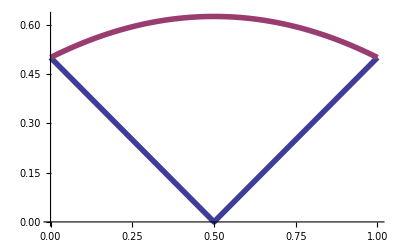
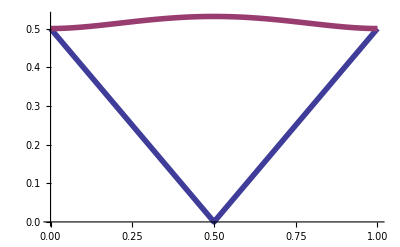
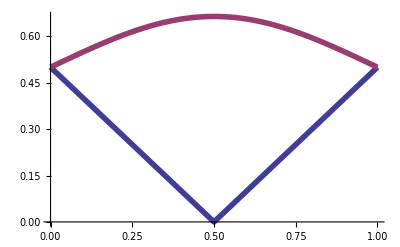
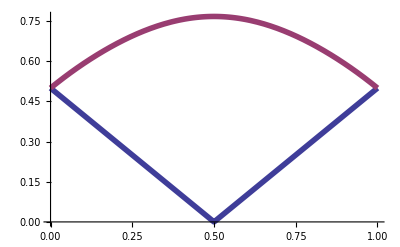
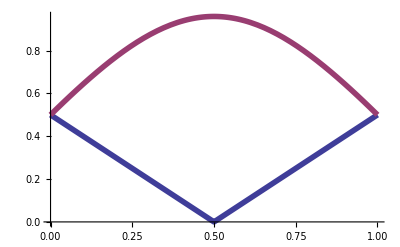
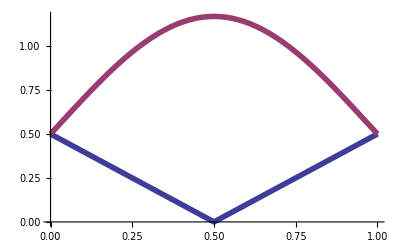
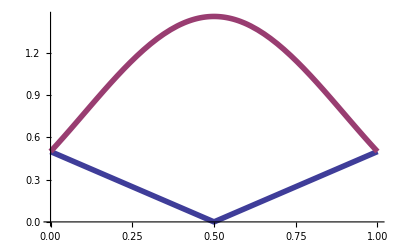
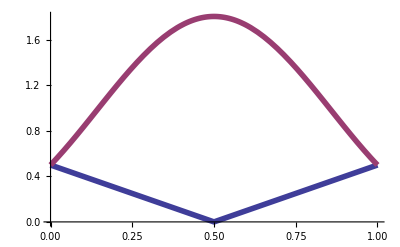

```mathematica
Table[P[x,k],{k,1,10}]
Table[Plot[{f[x],P[x,k]},{x,0,1},PlotRange->All,PlotStyle->{Thickness[0.01]}],{k,1,10}] 
Plot[f[x],{x,0,1}]
```

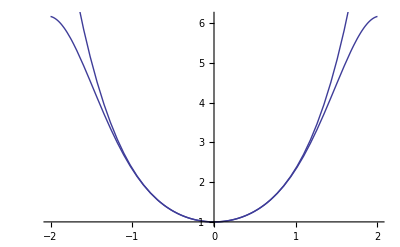

```mathematica
Show[Plot[Exp[x*Sin[x]],{x,-2,2}],Plot[Evaluate[Normal[Series[Exp[x*Sin[x]],{x,0,6}]]],{x,-2,2}]]
```

```mathematica
Series[Exp[x] Sqrt[1-x],{x,0,3}]
```

1+x/2-x^2/8-(13 x^3)/48+O[x]^4

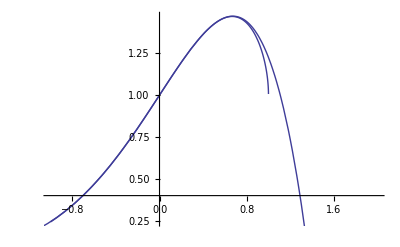

```mathematica
Show[Plot[Exp[x*Sqrt[1-x]],{x,-1,2}],Plot[Evaluate[Normal[Series[Exp[x*Sqrt[1-x]],{x,0,6}]]],{x,-2,2}]]
```